```mathematica
longitude = Range[65,115];
latitude = Range[30,50];
aeroid = Flatten@Table[ToString@i<>ToString@j,{i,latitude},{j,longitude}];
```

```mathematica
(*Table[GeoElevationData[{i,j}],{i,latitude},{j,longitude}]*)
```

```mathematica
(*Export["F:\\Godot\\silkway\\resouce\\data\\aero.res",Prepend[Transpose[{aeroid,First/@altitude}],{"id","altitude"}],"Table"]*)
```

#### 高度圖

```mathematica
reliefMap[lat_,long_]:= GeoGraphics[GeoPosition[{lat+0.5,long+0.5}],GeoRange->Quantity[55.5,"Kilometers"],GeoBackground->GeoStyling["ReliefMap"]];
```

```mathematica
plot3d[lat_,long_]:= ListPlot3D[Reverse@elevation[lat,long],MeshFunctions->{#3&},Mesh->30,ImageSize->Medium];
```

#### 海拔

```mathematica
elevation[lat_,long_]:= QuantityMagnitude[GeoElevationData[GeoPosition[Table[{i,j},{i,lat,lat+0.9,0.1},{j,long,long+0.9,0.1}]]]];
```

```mathematica
makeElevation [lat_,long_]:= Export[ToString@StringForm["F:\\Godot\\silkway\\resouce\\data\\elevation\\`1``2`.json",lat,long],elevation[lat,long],"JSON"];
```

```mathematica
(*Do[makeElevation[lat,long],{long,longitude},{lat,latitude}]*)
```

```mathematica
(#-Min[Mean@elevation[34,112]])&/@elevation[34,112]
```

{{422.,1040.,437.,309.,536.,238.,156.,186.,56.,-56.},{308.,154.,300.,116.,168.,105.,118.,20.,-34.,-100.},{266.,112.,46.,232.,333.,217.,26.,-31.,-42.,-6.},{487.,319.,44.,-36.,12.,54.,75.,212.,104.,211.},{291.,178.,85.,27.,-56.,-44.,82.,125.,179.,140.},{-46.,109.,-1.,58.,54.,-63.,183.,338.,320.,257.},{115.,112.,16.,-52.,-124.,-140.,-122.,-111.,-95.,84.},{172.,61.,1.,-89.,-110.,-132.,-154.,-159.,-162.,-162.},{188.,220.,64.,104.,59.,-19.,-88.,-100.,-162.,-93.},{265.,163.,-71.,67.,17.,-149.,-141.,-146.,-164.,-168.}}

```mathematica
IntegerPart[Divide[#,(Mean@Flatten@elevation[34,112])]]&/@(elevation[34,108])
```

{{5,4,4,4,3,4,3,1,2,3},{2,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,2,1,1,1,1,1,1,1,1},{2,2,2,2,2,1,1,1,1,1},{2,2,2,2,2,2,3,1,1,1},{3,3,2,3,2,2,2,2,1,1},{3,2,2,2,3,3,3,2,2,2}}

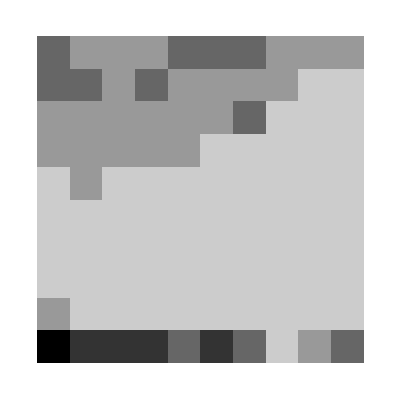

```mathematica
ArrayPlot[Reverse@%243]
```

```mathematica
IdentityMatrix[3].{a,b,c}
```

{a,b,c}

False